# 向量 RT0 体积 PEEC

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

(R+jωL)i+e=Cᵀv; Ci=b

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

选择外场或输运激励。外场算例为 1 mT RMS Bz、零净输运。

## 推导与结果解释

最低阶 Raviart–Thomas 面通量自由度表示具有单元散度的向量电流；相邻单元共享带方向的面通量，关联矩阵 C 实现离散电流连续性。

混合 PEEC 系统为 (R+jωL)i+e=Cᵀv、Ci=b。外场教程采用 Bz=1 mT RMS、零净输运，分别由重构电流与电阻二次型计算损耗。

检查真实线性残差、连续性、积分及空间敏感性。外场损耗是诊断量；用另设输运电流的平方去除它，不能据此定义内禀电阻。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"dimensions"->{2,2,3},"cell_width_m"->0.0005,"quadrature_order"->6,"excitation"->"field"|>;parameters
```

<|dimensions -> {2, 2, 3}, cell_width_m -> 0.0005, quadrature_order -> 6, 
 
>   excitation -> field|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"rt0",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_rt0_20261014075222_4c2f232e, 
 
>   source_model -> 3D_RT0_volume_face_flux_PEEC, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

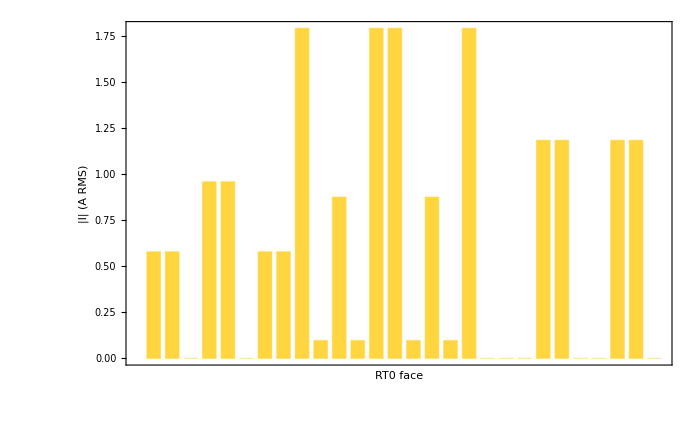

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: P03, RUEHLI1974, RT1977, GMRES1986; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch rt0